```mathematica
<<Local`QFTToolKit2`
Get[NotebookDirectory[]<>"1204.0328 ParticlePhysicsFromAlmostCommutativeSpacetime.3.out"];
$defCInv={};
```

```mathematica
"Notational definitions"
"Note that in the text the symbols may reference different Hilbert spaces. This has caused confusion in some of the calculations.  To address this problem we will try to label the variables by subscripts to designate the applicable Hilbert space.
NOTE: Need to do notational change for .1,.2 notebooks."

rghtA[a_]:=Superscript[a,o]
cl[a_]:=Subscript[⟨a⟩, cl];
clB[a_]:=Subscript[{a}, cl];
ct[a_]:=ConjugateTranspose[a];
cc[a_]:=Conjugate[a];
star[a_]:=Superscript[a,"*"];
cross[a_]:=Superscript[a,"×"];
deg[a_]:=|a|;
it[a_]:=Style[a,Italic]
iD:=it[D]
iA:=it[A]
iI:=it["I"]
C∞:=C^("∞")
Subscript[B, x_]:=T[B,"d",{x}]
Subscript[(("∇")^S), n_]:=T[("∇")^S,"d",{n}]
disjointQ[b_,c_,free_List:{u,d,e,ν,L,R}]:=Apply[Or,Map[FreeQ[b,#]&&!FreeQ[c,#]&,free]];

accumDef[item_]:=Block[{},$defall=tuAppendUniq[item][$defall];""];
accumStdMdl[item_]:=Block[{},$defStdMdl=tuAppendUniq[item][$defStdMdl];""];
accumCInv[item_]:=Block[{},$defCInv=tuAppendUniq[item][$defCInv];""];

selectStdMdl[heads_,with_:{},all_:Null]:=tuRuleSelect[$defStdMdl][Flatten[{heads}]]//Select[#,tuHasAllQ[#,Flatten[{with}]]&]&//If[all===Null,Last[#],#]&;
selectGWS[heads_,with_:{},all_:Null]:=tuRuleSelect[$defGWS][Flatten[{heads}]]//Select[#,tuHasAllQ[#,Flatten[{with}]]&]&//If[all===Null,Last[#],#]&;
selectDef[heads_,with_:{},all_:Null]:=tuRuleSelect[$defall][Flatten[{heads}]]//Select[#,tuHasAllQ[#,Flatten[{with}]]&]&//If[all===Null,Last[#],#]&;
selectCInv[heads_,with_:{},all_:Null]:=tuRuleSelect[$defCInv][Flatten[{heads}]]//Select[#,tuHasAllQ[#,Flatten[{with}]]&]&//If[all===Null,Last[#],#]&;

Clear[expandDC];
expandDC[sub_:{},scalar_:{}]:=tuRepeat[{sub,tuOpDistribute[Dot],tuOpSimplify[Dot,scalar],tuOpDistribute[CircleTimes]},tuCircleTimesSimplify]
Clear[expandCom]
expandCom[subs_:{}][exp_]:=Block[{tmp=exp},
tmp=tmp//.tuCommutatorExpand//expandDC[];
tmp=tmp/.toxDot//.Flatten[{subs}];
tmp=tmp//tuMatrixOrderedMultiply//(#/.toDot&)//expandDC[];
tmp
];
(**)
$sgeneral:={
T[γ,"d",{5}]->Product[T[γ,"u",{μ}],{μ,4}],
T[γ,"d",{5}].T[γ,"d",{5}]->1,ConjugateTranspose[T[γ,"d",{5}]]->T[γ,"d",{5}],CommutatorP[T[γ,"d",{5}],T[γ,"u",{μ}]]->0,T["∇","d",{_}][Subscript[1, n_]]->0,a_ . Subscript[1, n_]->a,Subscript[1, n_] . a_->a}
$sgeneral//ColumnBar

Clear[$symmetries]
$symmetries:={tt:T[g,"uu",{μ_,ν_}]:>tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}],
tt:T[F,"uu",{μ_,ν_}]:>-tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}],
tt:T[F,"dd",{μ_,ν_}]:>-tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}],
CommutatorM[a_,b_]:>-CommutatorM[b,a]/;OrderedQ[{b,a}],
CommutatorP[a_,b_]:>CommutatorP[b,a]/;OrderedQ[{b,a}],
tt:T[γ,"u",{μ}] . T[γ,"d",{5}] :>Reverse[tt]
};
$symmetries//ColumnBar

εRule[KOdim_Integer]:=Block[{n=Mod[KOdim,8],
table={{1,1,-1,-1,-1,-1,1,1},{1,-1,1,1,1,-1,1,1},{1,,-1,,1,,-1,}}},
{ε->table[[1,n+1]],ε'->table[[2,n+1]],ε''->table[[3,n+1]]}
]
εRule[6]

$transformVar=Map[#->OverTilde[#]&,{B,Φ,Λ,s,g,C,F,iD}];$transformVar//ColumnBar
```

Notational definitions

Note that in the text the symbols may reference different Hilbert spaces. This has caused confusion in some of the calculations.  To address this problem we will try to label the variables by subscripts to designate the applicable Hilbert space.
NOTE: Need to do notational change for .1,.2 notebooks.

γ_5^5→γ_1^1 γ_2^2 γ_3^3 γ_4^4
γ_5^5.γ_5^5→1
(γ_5^5)^†→γ_5^5
{γ_5^5,γ_μ^μ}_+→0
∇__^_ [1_n_]→0
(a_).1_n_→a
1_n_.(a_)→a

tt:g_μ_ν_^μ_ν_:>tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}]
tt:F_μ_ν_^μ_ν_:>-tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}]
tt:F_μ_ν_^μ_ν_:>-tuIndexSwap[{μ,ν}][tt]/;OrderedQ[{ν,μ}]
[a_,b_]_-:>-[b,a]_-/;OrderedQ[{b,a}]
{a_,b_}_+:>{b,a}_+/;OrderedQ[{b,a}]
tt:γ_μ^μ.γ_5^5:>Reverse[tt]

{ε→1,ε'→1,ε''→-1}

B→B̃
Φ→Φ̃
Λ→Λ̃
s→s̃
g→g̃
C→C̃
F→F̃
D→D̃

### 7. Conformal invariance

#### 7.1 Conformal Invariance

7.1.1 Conformal Transformation

```mathematica
PR["*Conformal transformation of metric: ",
$={T[g̃,"dd",{μ,ν}]->Ω^2 T[g,"dd",{μ,ν}],T[g̃,"uu",{μ,ν}]->Ω^(-2)  T[g,"uu",{μ,ν}],Ω∈(C^("∞"))[M,SuperPlus[ℝ]]},
NL,"Transformed Scalar curvature: ",
$e71={s̃->Ω^-2(s-2(m-1) tuDs["∇"][tuDsu["∇"][Log[Ω],β],β]-(m-1)(m-2) tuDs["∇"][Log[Ω],β]tuDsu["∇"][Log[Ω],β]),"∇"[CG["Levi-Civita connection"]]},
accumCInv[{$,$e71}];
]
```

*Conformal transformation of metric: {(g̃)_μν^μν→Ω^2 g_μν^μν,(g̃)_μν^μν→g_μν^μν/Ω^2,Ω∈C^∞[M,ℝ^+]}
Transformed Scalar curvature: {s̃→(s-2 (-1+m) UnderBar[∇]_β[UnderBar[∇]^β[Log[Ω]]]-(-2+m) (-1+m) UnderBar[∇]_β[Log[Ω]] UnderBar[∇]^β[Log[Ω]])/Ω^2,∇[Levi-Civita connection]}Null

7.1.2 Conformal gravity

```mathematica
PR["*Weyl action: ",
$sWeyl={Subscript[S, W][g_]->xIntegral[√Det[g] T[C,"dddd",{μ,ν,ρ,σ}]T[C,"uuuu",{μ,ν,ρ,σ}],x∈M],T[C,"uddd",{μ,ν,ρ,σ}][CG["Weyl tensor"]],T[C,"uddd",{μ,ν,ρ,σ}]->T[C̃,"uddd",{μ,ν,ρ,σ}]},
accumCInv[$sWeyl];
NL,"●Proposition 7.1: Weyl action is conformally invariant for dim[M]→4. ",
line,
NL,"Examine ",$=$sWeyl//tuExtractIntegrand,
NL,"•Since ",$=(T[C,"dddd",{μ,ν,ρ,σ}]->T[g,"dd",{μ,α}]T[C,"uddd",{α,ν,ρ,σ}]/.$transformVar),
accumCInv[$];
" and ",$s={
{selectCInv[T[g̃,"dd",{_,_}]]}//tuAddPatternVariable[{μ,ν}],
tuRuleSelect[$sWeyl][T[C,"uddd",{μ,ν,ρ,σ}]]//First//Reverse//tuAddPatternVariable[{μ,ν,ρ,σ}]}//Flatten;$s//ColumnBar,
Yield,$=$/.$s,
Yield,$1=$=$//tuMetricContractAll[g];$1//Framed,
NL,"Since ",$s=T[g,"uu",{μ1,μ}]T[g,"uu",{ν1,ν}]T[g,"uu",{ρ1,ρ}]T[g,"uu",{σ1,σ}]T[C_,"dddd",{μ,ν,ρ,σ}]->T[C,"uuuu",{μ1,ν1,ρ1,σ1}]//tuAddPatternVariable[{μ,ν,σ,ρ,g}],
NL,"Apply common multiplier, definition of g, contraction,: ",
Yield,$=(T[g,"uu",{μ1,μ}]T[g,"uu",{ν1,ν}]T[g,"uu",{ρ1,ρ}]T[g,"uu",{σ1,σ}]/.g->g̃)#&/@$,
Yield,$[[1]]=$[[1]]//tuMetricContractAll[g̃];$,
Yield,$=$/.{selectCInv[T[g̃,"uu",{_,_}]]//tuAddPatternVariable[{μ,ν}]},
Yield,$2=$=$//tuMetricContractAll[g];
$2=$=$/.{μ1->μ,ν1->ν,ρ1->ρ,σ1->σ};$2//Framed,
NL,"From ",
$=($d=Det[g]->T[ϵ,"uuuu",{μ,ν,ρ,σ}]T[g,"dd",{1,μ}]T[g,"dd",{2,ν}]T[g,"dd",{3,ρ}]T[g,"dd",{4,σ}])/.g->g̃,
Yield,$=$/.(selectCInv[T[g̃,"dd",{_,_}]]//tuAddPatternVariable[{μ,ν}]),
Yield,$=$/.Reverse[$d],
Yield,$3=$=Sqrt[#]&/@$//PowerExpand,
NL,
Yield,$={$1,$2,$3};$//ColumnBar,
NL,"Taking the product ",
$=$//tuRuleOp[Times];$//Framed,
accumCInv[{$,$1,$2,$3}]
]
```

*Weyl action: {S_W[g_]→√Det[g] C_μνρσ^μνρσ C_μνρσ^μνρσx∈M,C_μνρσ^μνρσ[Weyl tensor],C_μνρσ^μνρσ→(C̃)_μνρσ^μνρσ}
●Proposition 7.1: Weyl action is conformally invariant for dim[M]→4. 
————————————————————————————————————————————————————————————
Examine {1,2,1}→√Det[g] C_μνρσ^μνρσ C_μνρσ^μνρσ
•Since (C̃)_μνρσ^μνρσ→(C̃)_ανρσ^ανρσ (g̃)_μα^μα and (g̃)_μ_ν_^μ_ν_→Ω^2 g_μν^μν
(C̃)_μ_ν_ρ_σ_^μ_ν_ρ_σ_→C_μνρσ^μνρσ
→ (C̃)_μνρσ^μνρσ→Ω^2 C_ανρσ^ανρσ g_μα^μα
→ (C̃)_μνρσ^μνρσ→Ω^2 C_μνρσ^μνρσ
Since C__μ_ν_ρ_σ_^μ_ν_ρ_σ_ g__μ1μ_^μ1μ_ g__ν1ν_^ν1ν_ g__ρ1ρ_^ρ1ρ_ g__σ1σ_^σ1σ_→C_μ1ν1ρ1σ1^μ1ν1ρ1σ1
Apply common multiplier, definition of g, contraction,: 
→ (C̃)_μνρσ^μνρσ (g̃)_μ1μ^μ1μ (g̃)_ν1ν^ν1ν (g̃)_ρ1ρ^ρ1ρ (g̃)_σ1σ^σ1σ→Ω^2 C_μνρσ^μνρσ (g̃)_μ1μ^μ1μ (g̃)_ν1ν^ν1ν (g̃)_ρ1ρ^ρ1ρ (g̃)_σ1σ^σ1σ
→ (C̃)_μ1ν1ρ1σ1^μ1ν1ρ1σ1→Ω^2 C_μνρσ^μνρσ (g̃)_μ1μ^μ1μ (g̃)_ν1ν^ν1ν (g̃)_ρ1ρ^ρ1ρ (g̃)_σ1σ^σ1σ
→ (C̃)_μ1ν1ρ1σ1^μ1ν1ρ1σ1→(C_μνρσ^μνρσ g_μ1μ^μ1μ g_ν1ν^ν1ν g_ρ1ρ^ρ1ρ g_σ1σ^σ1σ)/Ω^6
→ (C̃)_μνρσ^μνρσ→C_μνρσ^μνρσ/Ω^6
From Det[g̃]→ϵ_μνρσ^μνρσ (g̃)_(1μ)^(1μ) (g̃)_(2ν)^(2ν) (g̃)_(3ρ)^(3ρ) (g̃)_(4σ)^(4σ)
→ Det[g̃]→Ω^8 g_(1μ)^(1μ) g_(2ν)^(2ν) g_(3ρ)^(3ρ) g_(4σ)^(4σ) ϵ_μνρσ^μνρσ
→ Det[g̃]→Ω^8 Det[g]
→ √Det[g̃]→Ω^4 √Det[g]

→ (C̃)_μνρσ^μνρσ→Ω^2 C_μνρσ^μνρσ
(C̃)_μνρσ^μνρσ→C_μνρσ^μνρσ/Ω^6
√Det[g̃]→Ω^4 √Det[g]
Taking the product √Det[g̃] (C̃)_μνρσ^μνρσ (C̃)_μνρσ^μνρσ→√Det[g] C_μνρσ^μνρσ C_μνρσ^μνρσ

#### 7.2 Conformal symmetry breaking

```mathematica
PR["*For field transforming as ",{ϕ->Ω^-1 ϕ,ϕ∈ℝ},
NL,"Invariant action for ϕ: ",
$action={S[T[g,"dd",{μ,ν}],ϕ]->xIntegral[√Det[g] (tuDPartial[ϕ,μ]tuDPartialu[ϕ,μ]/2+s ϕ^2/12+λ ϕ^4),x∈M],s<0,λ>0},
NL,"Minimum of Potential: ",$lagrange=$=$action//tuExtractIntegrand,
Yield,$=V->$[[2]]//(#/.{√_->1,tuDPartial[ϕ,μ]->0})&,
Yield,$=(#->0&)/@(tuDPartial[#,ϕ]&/@$),
imply,$=$[[2]]//tuDerivativeExpand[{s,λ}]//tuRuleSolve[#,ϕ]&//Last,
NL,"Vacuum expectation value: v→ ",$vev=$=Map[#^2&,$];$//Framed
];
```

*For field transforming as {ϕ→ϕ/Ω,ϕ∈ℝ}
Invariant action for ϕ: {S[g_μν^μν,ϕ]→√Det[g] ((s ϕ^2)/12+λ ϕ^4+1/2 UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ])x∈M,s<0,λ>0}
Minimum of Potential: {1,2,1}→√Det[g] ((s ϕ^2)/12+λ ϕ^4+1/2 UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ])
→ V→(s ϕ^2)/12+λ ϕ^4
→ (UnderBar[∂]_ϕ[V]→0)→UnderBar[∂]_ϕ[(s ϕ^2)/12+λ ϕ^4]→0 ⇒ ϕ→(ⅈ √s)/(2 √6 √λ)
Vacuum expectation value: v→ ϕ^2→-s/(24 λ)

```mathematica
PR["*If scalar curvature(s) not constant, kinetic terms of Lagrangian need to be consider to find vacuum expectation value: ",$L=$=ℒ->$lagrange[[2,2]],
NL,"Direct solution of the Euler-Lagrange equation to find extremum(apply Mathematica EulerLagrange): ",
Yield,$=$L/.ϕ->ϕ[x]/.tuDPartial[a_,μ_]:>D[a,x]/.tuDPartialu[a_,μ_]:>D[a,x],
Yield,($=EulerEquations[$[[2]],ϕ[x],x])//D2xPartialD[]//(#/.ϕ[x]->ϕ/.x->μ)&,
NL,"Mathematica's solution is complex: ","POFF",
Yield,DSolve[$,ϕ[x],x]
];
```

*If scalar curvature(s) not constant, kinetic terms of Lagrangian need to be consider to find vacuum expectation value: ℒ→(s ϕ^2)/12+λ ϕ^4+1/2 UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ]
Direct solution of the Euler-Lagrange equation to find extremum(apply Mathematica EulerLagrange): 
→ ℒ→1/12 s ϕ[x]^2+λ ϕ[x]^4+1/2 ϕ'[x]^2
→ (s ϕ)/6+4 λ ϕ^3-UnderBar[∂]_μ[UnderBar[∂]_μ[ϕ]]==0
Mathematica's solution is complex:

```mathematica
PR["*Apply conformal invariance of the Higgs potential: ",
NL,"If we apply: ",$s={s->Ω^2 Subscript[s, 0][CG["constant"]]},
Yield,$=$Lt=$L/.tuRule[$s];CR[$,back,"ϕ is now transformed."],
NL,"Then the vacuum expectation value (minimum potential) of: ",
Yield,$=V->$[[2]]/.{tuDPartial[_,_]->0},

Yield,$=(#->0&)/@(tuDPartial[#,ϕ]&/@$),
imply,$=$[[2]]//tuDerivativeExpand[{Subscript[s, 0],λ,Ω}]//tuRuleSolve[#,ϕ]&//Last,
NL,"Vacuum expectation value: ",$vev=$=Map[#^2&,$]/.ϕ->Subscript[v, 0];$//Framed,CR[" not constant?"],

NL,"Investigate transformed: ",$s=ϕ->(Subscript[v, 0]+h)/Ω,
Yield,$=$Lt/.$s,
NL,"Constants: ",$s={Subscript[s, 0],Subscript[v, 0],Ω},
Yield,$=$//tuDerivativeExpand[$s],
NL,"Letting: ",$s={tuRuleSolve[$vev,Subscript[s, 0]],Ω->1}//Flatten,
Yield,$=$//.$s//Expand//Collect[#,λ]&;$//Framed
]
```

*Apply conformal invariance of the Higgs potential: 
If we apply: {s→Ω^2 s_0[constant]}
→ ℒ→λ ϕ^4+1/12 ϕ^2 Ω^2 s_0+1/2 UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ] ⟵ϕ is now transformed.
Then the vacuum expectation value (minimum potential) of: 
→ V→λ ϕ^4+1/12 ϕ^2 Ω^2 s_0
→ (UnderBar[∂]_ϕ[V]→0)→UnderBar[∂]_ϕ[λ ϕ^4+1/12 ϕ^2 Ω^2 s_0]→0 ⇒ ϕ→(ⅈ Ω √s_0)/(2 √6 √λ)
Vacuum expectation value: v_0^2→-(Ω^2 s_0)/(24 λ) not constant?
Investigate transformed: ϕ→(h+v_0)/Ω
→ ℒ→1/12 s_0 (h+v_0)^2+(λ (h+v_0)^4)/Ω^4+1/2 UnderBar[∂]_μ[(h+v_0)/Ω] UnderBar[∂]^μ[(h+v_0)/Ω]
Constants: {s_0,v_0,Ω}
→ ℒ→1/12 s_0 (h+v_0)^2+(λ (h+v_0)^4)/Ω^4+(UnderBar[∂]_μ[h] UnderBar[∂]^μ[h])/(2 Ω^2)
Letting: {s_0→-(24 λ v_0^2)/Ω^2,Ω→1}
→ ℒ→λ (h^4+4 h^3 v_0+4 h^2 v_0^2-v_0^4)+1/2 UnderBar[∂]_μ[h] UnderBar[∂]^μ[h]

#### 7.3 Conformal transformations of the spectral action

```mathematica
PR["*From (2.16-.17): ",
CO[$={selectDef[T[γ,"d",{5}]⊗_]/.(εRule[KOdim]/.selectStdMdl[KOdim])//.tuOpDistribute[CircleTimes]//Reverse,
selectDef[T[γ,"u",{μ}]⊗_]/.(εRule[KOdim]/.selectStdMdl[KOdim])//Reverse
}],
NL,
$e216x7=$={T[γ,"d",{5}]⊗Φ->T[γ,"d",{5}]⊗Subscript[𝒟, F]+T[γ,"d",{5}]⊗ϕ+J.(T[γ,"d",{5}] ⊗ ϕ) . ct[J],
T[γ,"u",{μ}]⊗T[B,"d",{μ}]->T[γ,"u",{μ}]⊗(T[A,"d",{μ}]-Subscript[J, F]. T[A,"d",{μ}] . ct[Subscript[J, F]])};$//ColumnBar,

NL,"With Conformal transformations: ",
$ct={T[B,"d",{μ}]->T[B,"d",{μ}],Φ->Φ/Ω,Λ->Λ/Ω,(**)
tuDUp[iD][a_,b_]->tuDUp[iD][a,b]/Ω^2,
tuDDown[iD][a_,b_]->tuDDown[iD][a,b],
tuExtractIntegrand[$sWeyl][[2]]->tuExtractIntegrand[$sWeyl][[2]],
T[F,"uu",{μ,ν}]->Ω^-4 T[F,"uu",{μ,ν}],
T[F,"dd",{μ,ν}]->T[F,"dd",{μ,ν}]
};
$ct=Map[(#[[1]]/.$transformVar)->#[[2]]&,$ct];
$ct=Append[$ct,selectCInv[Sqrt[Det[g̃]]]];
$ct//ColumnBar,

line,
NL,"●Proposition 7.3: Conformal transform of the spectral action is: ",
NL,ℒ[T[g̃,"dd",{μ,ν}],T[B̃,"d",{μ}],Φ̃,Λ̃]->ℒ[T[g,"dd",{μ,ν}],T[B,"d",{μ}],Φ,Λ]+N Subscript[f, 2] Λ^2/(Ω^2 4 π^2) tuDsu["∇"][Ω,β]tuDs["∇"][Ω,β] √Det[g]
]
PR["• Proof: Transform the ℒ terms of Proposition 3.7 ",tuRuleSelect[$p37][ℒ[__]][[1]],
line,
NL,CO[">The Transform of (3.19): "],
CR["(ignoring topological and boundary terms in Proposition 3.7)"],
$=$=$e319=Subscript[ℒ, M][T[g,"dd",{μ,ν}]]->Subscript[f, 4] Λ^4/(2π^2)-s Subscript[f, 2] Λ^2/(24π^2)-f[0]/(480π^2) T[C,"dddd",{μ,ν,ρ,σ}]T[C,"uuuu",{μ,ν,ρ,σ}];
$=Sqrt[Det[g]]#&/@$//Expand;
$=$/.$transformVar;
Imply,$[[2]]=$[[2]]/.tuRule[$e71]//.$ct//Expand//tuDerivativeExpand[];
$//ColumnSumExp,(**)

NL,"Let: ",$s={m->4},
Yield,$=MapAt[#/.$s&,$,2],
NL,"Subtract 3.19 to evaluate difference: ",$s=√Det[g]#&/@$e319,
Yield,$=tuRuleSubtract[{$,$s}]//Expand//Simplify;$//ColumnSumExp//Framed;
NL,"The Transformed (3.19): ",
$a1=$=tuRuleSolve[$,$[[1,2]]][[1]]//Expand;$//Framed
];

PR[CO[">The Transform of (3.19) : "],$=tuRuleSelect[$p37][Subscript[ℒ, B][_]][[1]];
$=($0=√Det[g]#&/@$)/.$transformVar//Expand,
Yield,$[[2]]=$[[2]]/.$ct/.selectCInv[Sqrt[Det[_]]]//tuTrSimplify[{Ω}];
$,
Yield,$a2=$=$/.Reverse[$0];$//Framed
];
PR[(*for Consistent notation*)
$sDc={T[iD_,"u",{μ_}][a_]->tuDUp[iD][a,μ],T[iD_,"d",{μ_}][a_]->tuDDown[iD][a,μ]};
CO[">The Transform of: "],$=tuRuleSelect[$p37][Subscript[ℒ, H][__]][[1]]/.s[x]->s;
$0=$=√Det[g]#&/@$/.$sDc;
$=$/.$transformVar,
NL,"For ",$s0={Δ[__]->0,m->4},

Yield,$[[2]]=$[[2]]/.tuRule[$e71]/.selectCInv[Sqrt[Det[_]]];$[[2]]=$[[2]]/.$s0//.$ct/.β->μ//.tuOpSimplify[Dot,{Ω}]//tuTrSimplify[{Ω}]//Expand;
$1=$;
$//ColumnSumExp,
NL,"•Examine the difference between the transformed and untransformed equations, ignoring boundary terms: ",
Yield,$=tuRuleSubtract[{$1,$0}]/.$s0//Expand//Simplify;
$//ColumnSumExp,
Yield,$=$//tuDerivativeExpand[]//Simplify//tuOpSimplifyF[Dot,{Ω}];$//ColumnSumExp,
NL,"Simplify ",
$=$/.Dot->Times//.tuOpSimplify[Tr,{Ω}]//ExpandAll;
$=$/.Tr[a_]:>Tr[tuIndexDummyOrdered[a]]//.tuOpDistribute[Tr]//Simplify;
NL,"Assume differential equivalent ",$s="∇"->iD,
Yield,$=$/.$s//.tuOpSimplify[Tr,{Ω,tuDUp[_][Ω,μ],tuDDown[_][Ω,μ]}];$//ColumnSumExp,

$=$/.{ Tr[Φ (dd:tuDUp[_])[Φ,μ]]->Tr[dd[Φ^2,μ]]/2}//Expand;$=$//Collect[#,Sqrt[_]f[0]]&;
$//ColumnSumExp,
NL,"The total differential of ",
$s=tuDUp[iD][Tr[Φ^2]tuDDown[iD][Ω,μ]/Ω,μ];
$s=0->($s//tuDerivativeExpand[]);
$s=tuRuleSolve[$s,$s[[2,1,2;;-1]]],
Yield,$=$/.$s//Expand;
$=$/.{tuDUp[iD][Tr[a_],μ_]->Tr[tuDUp[iD][a,μ]]}//tuIndexDummyOrdered,
$a3=$=$[[1,2]]->-$[[1,1]];
$//ColumnSumExp
];
PR["• Summing these term: ",$={$a1,$a2,$a3}//Flatten//tuRuleAdd;
Yield,
$=$/.$s//tuIndexDummyOrdered//ColumnSumExp,
NL,"Proves the Proposition."
]
```

*From (2.16-.17): {γ_5^5⊗Φ→γ_5^5⊗ϕ+γ_5^5⊗J_F.ϕ.(J_F)^†+γ_5^5⊗D_F,γ_μ^μ⊗B_μ^μ→γ_μ^μ⊗(-J_F.A_M_μ^μ.(J_F)^†+A_M_μ^μ)}
γ_5^5⊗Φ→γ_5^5⊗ϕ+γ_5^5⊗𝒟_F+J.(γ_5^5⊗ϕ).J^†
γ_μ^μ⊗B_μ^μ→γ_μ^μ⊗(-J_F.A_μ^μ.(J_F)^†+A_μ^μ)
With Conformal transformations: (B̃)_μ^μ→B_μ^μ
Φ̃→Φ/Ω
Λ̃→Λ/Ω
UnderBar[D̃]^b_[a_]→(D̲)^b[a]/Ω^2
UnderBar[D̃]_b_[a_]→(D̲)_b[a]
√Det[g̃] (C̃)_μνρσ^μνρσ (C̃)_μνρσ^μνρσ→√Det[g] C_μνρσ^μνρσ C_μνρσ^μνρσ
(F̃)_μν^μν→F_μν^μν/Ω^4
(F̃)_μν^μν→F_μν^μν
√Det[g̃]→Ω^4 √Det[g]
————————————————————————————————————————————————————————————
●Proposition 7.3: Conformal transform of the spectral action is: 
ℒ[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃,Λ̃]→ℒ[g_μν^μν,B_μ^μ,Φ,Λ]+(N Λ^2 √Det[g] f_2 UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/(4 π^2 Ω^2)

• Proof: Transform the ℒ terms of Proposition 3.7 ℒ[g_μν^μν,B_μ^μ,Φ]→ℒ_B[B_μ^μ]+ℒ_H[g_μν^μν,B_μ^μ,Φ]+N ℒ_M[g_μν^μν]
————————————————————————————————————————————————————————————
>The Transform of (3.19): (ignoring topological and boundary terms in Proposition 3.7)
⇒ √Det[g̃] ℒ_M[(g̃)_μν^μν]→∑[-(s Λ^2 √Det[g] f_2)/(24 π^2)
(Λ^4 √Det[g] f_4)/(2 π^2)
-(√Det[g] f[0] C_μνρσ^μνρσ C_μνρσ^μνρσ)/(480 π^2)
(Λ^2 √Det[g] f_2 UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/(12 π^2 Ω^2)
-(m Λ^2 √Det[g] f_2 UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/(8 π^2 Ω^2)
(m^2 Λ^2 √Det[g] f_2 UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/(24 π^2 Ω^2)
-(Λ^2 √Det[g] f_2 ((UnderBar[∇]_β[UnderBar[∇]^β[Ω]])/Ω-(UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/Ω^2))/(12 π^2)
(m Λ^2 √Det[g] f_2 ((UnderBar[∇]_β[UnderBar[∇]^β[Ω]])/Ω-(UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/Ω^2))/(12 π^2)]
Let: {m→4}
→ √Det[g̃] ℒ_M[(g̃)_μν^μν]→-(s Λ^2 √Det[g] f_2)/(24 π^2)+(Λ^4 √Det[g] f_4)/(2 π^2)-(√Det[g] f[0] C_μνρσ^μνρσ C_μνρσ^μνρσ)/(480 π^2)+(Λ^2 √Det[g] f_2 UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/(4 π^2 Ω^2)+(Λ^2 √Det[g] f_2 ((UnderBar[∇]_β[UnderBar[∇]^β[Ω]])/Ω-(UnderBar[∇]_β[Ω] UnderBar[∇]^β[Ω])/Ω^2))/(4 π^2)
Subtract 3.19 to evaluate difference: √Det[g] ℒ_M[g_μν^μν]→√Det[g] (-(s Λ^2 f_2)/(24 π^2)+(Λ^4 f_4)/(2 π^2)-(f[0] C_μνρσ^μνρσ C_μνρσ^μνρσ)/(480 π^2))
→ 
The Transformed (3.19): √Det[g̃] ℒ_M[(g̃)_μν^μν]→√Det[g] ℒ_M[g_μν^μν]+(Λ^2 √Det[g] f_2 UnderBar[∇]_β[UnderBar[∇]^β[Ω]])/(4 π^2 Ω)

>The Transform of (3.19) : √Det[g̃] ℒ_(B̃)[(B̃)_μ^μ]→(√Det[g̃] f[0] Tr[(F̃)_μν^μν (F̃)_μν^μν])/(24 π^2)
→ √Det[g̃] ℒ_(B̃)[(B̃)_μ^μ]→(√Det[g] f[0] Tr[F_μν^μν F_μν^μν])/(24 π^2)
→ √Det[g̃] ℒ_(B̃)[(B̃)_μ^μ]→√Det[g] ℒ_B[B_μ^μ]

>The Transform of: √Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]→√Det[g̃] ((f[0] s̃ Tr[Φ̃.Φ̃])/(48 π^2)-((Λ̃)^2 f_2 Tr[Φ̃.Φ̃])/(2 π^2)+(f[0] Tr[UnderBar[D̃]_μ[Φ̃].UnderBar[D̃]^μ[Φ̃]])/(8 π^2)+(f[0] Tr[Φ̃.Φ̃.Φ̃.Φ̃])/(8 π^2)+(f[0] Δ[Tr[Φ̃.Φ̃]])/(24 π^2))
For {Δ[__]→0,m→4}
→ √Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]→∑[(s √Det[g] f[0] Tr[Φ.Φ])/(48 π^2)
-(Λ^2 √Det[g] f_2 Tr[Φ.Φ])/(2 π^2)
(Ω^2 √Det[g] f[0] Tr[(D̲)_μ[Φ/Ω].(D̲)^μ[Φ/Ω]])/(8 π^2)
(√Det[g] f[0] Tr[Φ.Φ.Φ.Φ])/(8 π^2)
-(√Det[g] f[0] Tr[Φ.Φ] UnderBar[∇]_μ[UnderBar[∇]^μ[Log[Ω]]])/(8 π^2)
-(√Det[g] f[0] Tr[Φ.Φ] UnderBar[∇]_μ[Log[Ω]] UnderBar[∇]^μ[Log[Ω]])/(8 π^2)]
•Examine the difference between the transformed and untransformed equations, ignoring boundary terms: 
→ ∑[-√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]
√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]]→-(∑[Tr[(D̲)_μ[Φ].(D̲)^μ[Φ]]
-Ω^2 Tr[(D̲)_μ[Φ/Ω].(D̲)^μ[Φ/Ω]]
Tr[Φ.Φ] (UnderBar[∇]_μ[UnderBar[∇]^μ[Log[Ω]]]+UnderBar[∇]_μ[Log[Ω]] UnderBar[∇]^μ[Log[Ω]])] √Det[g] f[0])/(8 π^2)
→ ∑[-√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]
√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]]→(∑[-Ω Tr[(D̲)_μ[Φ].(D̲)^μ[Φ]]
Ω^3 Tr[((Ω (D̲)_μ[Φ]-Φ (D̲)_μ[Ω]).(Ω (D̲)^μ[Φ]-Φ (D̲)^μ[Ω]))/Ω^4]
-Tr[Φ.Φ] UnderBar[∇]_μ[UnderBar[∇]^μ[Ω]]] √Det[g] f[0])/(8 π^2 Ω)
Simplify 
Assume differential equivalent ∇→D
→ ∑[-√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]
√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]]→-(∑[2 Ω Tr[Φ (D̲)^μ[Φ]] (D̲)_μ[Ω]
Ω Tr[Φ^2] (D̲)_μ[(D̲)^μ[Ω]]
-Tr[Φ^2] (D̲)_μ[Ω] (D̲)^μ[Ω]] √Det[g] f[0])/(8 π^2 Ω^2)∑[-√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]
√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]]→∑[-(Tr[(D̲)^μ[Φ^2]] (D̲)_μ[Ω])/(8 π^2 Ω)
-(Tr[Φ^2] (D̲)_μ[(D̲)^μ[Ω]])/(8 π^2 Ω)
(Tr[Φ^2] (D̲)_μ[Ω] (D̲)^μ[Ω])/(8 π^2 Ω^2)] √Det[g] f[0]
The total differential of {(Tr[Φ^2] (D̲)_μ[Ω] (D̲)^μ[Ω])/Ω^2→((D̲)_μ[Ω] (D̲)^μ[Tr[Φ^2]]+Tr[Φ^2] (D̲)^μ[(D̲)_μ[Ω]])/Ω}
→ -√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]+√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]→0√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]→√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]

• Summing these term: 
→ ∑[√Det[g̃] ℒ_H[(g̃)_μν^μν,(B̃)_μ^μ,Φ̃]
√Det[g̃] ℒ_M[(g̃)_μν^μν]
√Det[g̃] ℒ_(B̃)[(B̃)_μ^μ]]→∑[√Det[g] ℒ_B[B_μ^μ]
√Det[g] ℒ_H[g_μν^μν,B_μ^μ,Φ]
√Det[g] ℒ_M[g_μν^μν]
(Λ^2 √Det[g] f_2 UnderBar[∇]_β[UnderBar[∇]^β[Ω]])/(4 π^2 Ω)]
Proves the Proposition.

#### 7.4 The Higgs mechanims revisited(GWS model with variable scalar curvature)

```mathematica
PR["● From the GWS model (5.17): ",$=tuTermExtract[H][selectGWS[Subscript[ℒ, H][__],{H'}]]/.H'->H;
NL,"• Transform variables so EulerEquations[] can be applied: ",
$s={Abs[H]->h[x],Abs[tuDDown[OverTilde[iD]][H,μ]]->D[h[x],x],s->s[x]},

Yield,$=$/.$s,
NL,"Apply EulerEquations: ",
Yield,$=EulerEquations[$,h[x],x];
Yield,$=$//tuD2tuDOp[tuDDown["∂"]];
$=(#/2&/@First[tuRuleSolve[$,tuDDown["∂"][tuDDown["∂"][h[x],x],x]]])//Simplify;

$//ColumnSumExp,CR["←b/a term different from text p.85."],

line,
NL,"See if action in invarient: Apply Conformal transform: ",
tuRuleSelect[$ct][Φ̃]⇒{H->H/Ω},
Imply,$s={h[x]->h[x]/Ω,Ω->Subscript[Ω, 0] √((2 a Subscript[f, 2] Λ^2-e f[0])/(a f[0])-s[x]/12)},

Yield,$=$/.$s[[1]],
Yield,$=$//tuDerivativeExpand[{Λ,f[0],a,Subscript[f, 2],Subscript[Ω, 0]}],
$=tuRuleSolve[$,tuDDown["∂"][tuDDown["∂"][h[x],x],x]]//First//Simplify;
$//ColumnSumExp,
NL,"If we substitute the above ",$s[[2]],
and,"take as constant ",$const={Λ,f[0],a,Subscript[f, 2],Subscript[Ω, 0],e},
Yield,$=$/.$s[[2]]//tuDerivativeExpand[$const]//Simplify;
$//ColumnSumExp,
CR["? Does not seem to be simple relationship for h[x] as in text for ṽ[x]. "]

]
```

● From the GWS model (5.17): 
• Transform variables so EulerEquations[] can be applied: {Abs[H]→h[x],Abs[UnderBar[D̃]_μ[H]]→h'[x],s→s[x]}
→ (b f[0] h[x]^4)/(2 π^2)+(a f[0] h[x]^2 s[x])/(12 π^2)+(h[x]^2 (e f[0]-2 a Λ^2 f_2))/π^2+(a f[0] h'[x]^2)/(2 π^2)
Apply EulerEquations: 
→ 
→ 1/2 UnderBar[∂]_x[UnderBar[∂]_x[h[x]]]→∑[e/a
(b h[x]^2)/a
s[x]/12
-(2 Λ^2 f_2)/f[0]] h[x]←b/a term different from text p.85.
————————————————————————————————————————————————————————————
See if action in invarient: Apply Conformal transform: {Φ̃→Φ/Ω}⇒{H→H/Ω}
⇒ {h[x]→h[x]/Ω,Ω→√(-s[x]/12+(-e f[0]+2 a Λ^2 f_2)/(a f[0])) Ω_0}
→ 1/2 UnderBar[∂]_x[UnderBar[∂]_x[h[x]/Ω]]→(h[x] (e/a+(b h[x]^2)/(a Ω^2)+s[x]/12-(2 Λ^2 f_2)/f[0]))/Ω
→ 1/2 (-(2 UnderBar[∂]_x[Ω] UnderBar[∂]_x[h[x]])/Ω^2+h[x] ((2 (UnderBar[∂]_x[Ω])^2)/Ω^3-(UnderBar[∂]_x[UnderBar[∂]_x[Ω]])/Ω^2)+(UnderBar[∂]_x[UnderBar[∂]_x[h[x]]])/Ω)→(h[x] (e/a+(b h[x]^2)/(a Ω^2)+s[x]/12-(2 Λ^2 f_2)/f[0]))/ΩUnderBar[∂]_x[UnderBar[∂]_x[h[x]]]→∑[(2 b h[x]^3)/(a Ω^2)
(2 UnderBar[∂]_x[Ω] UnderBar[∂]_x[h[x]])/Ω
h[x] ((2 e)/a+s[x]/6-(4 Λ^2 f_2)/f[0]-(2 (UnderBar[∂]_x[Ω])^2)/Ω^2+(UnderBar[∂]_x[UnderBar[∂]_x[Ω]])/Ω)]
If we substitute the above Ω→√(-s[x]/12+(-e f[0]+2 a Λ^2 f_2)/(a f[0])) Ω_0 and take as constant {Λ,f[0],a,f_2,Ω_0,e}
→ UnderBar[∂]_x[UnderBar[∂]_x[h[x]]]→∑[-(24 b f[0] h[x]^3)/((12 e f[0]+a f[0] s[x]-24 a Λ^2 f_2) Ω_0^2)
(a f[0] UnderBar[∂]_x[h[x]] UnderBar[∂]_x[s[x]])/(12 e f[0]+a f[0] s[x]-24 a Λ^2 f_2)
h[x] ((2 e)/a+s[x]/6-(4 Λ^2 f_2)/f[0]-(3 a^2 f[0]^2 (UnderBar[∂]_x[s[x]])^2)/(4 (12 e f[0]+a f[0] s[x]-24 a Λ^2 f_2)^2)+(a f[0] UnderBar[∂]_x[UnderBar[∂]_x[s[x]]])/(24 e f[0]+2 a f[0] s[x]-48 a Λ^2 f_2))]? Does not seem to be simple relationship for h[x] as in text for ṽ[x].

Theorem 7.6

```mathematica
PR["Theorem 7.6: The gauge and conformal transformations: ",
$sH=$={H->u[x]/Ω[x]{{Subscript[v, 0]+h[x]},{0}},h[x_]->Ω[x]Abs[H[x]]-Subscript[v, 0]};$//MatrixForms//ColumnBar,
NL,"break gauge and conformal symmetry.  Broken bosonic action (GWS) is: ",
$=Subscript[S, B]->IntegralOp[{{x∈M}},√Det[g](4 Subscript[f, 4] Λ^4/(π^2)-c  Subscript[f, 2] Λ^2/(π^2)+d f[0]/(4π^2)-b π^2 Subscript[v, 0]^4/(2 a^2 f[0])+(c f[0]/(24π^2)-Subscript[f, 2] Λ^2/(3π^2))s-f[0]/(40π^2)T[C,"dddd",{μ,ν,ρ,σ}]T[C,"uuuu",{μ,ν,ρ,σ}]
+T[B,"dd",{μ,ν}]T[B,"uu",{μ,ν}]/4
+T[W,"udd",{a,μ,ν}]T[W,"uuu",{a,μ,ν}]/4
+Subscript[f, 2] Λ^2/(3π^2)tuDPartial[η,β]tuDPartialu[η,β]
+tuDPartial[h,β]tuDPartialu[h,β]/2
+bπ^2/(2 a^2 f[0])(h^4+4 Subscript[v, 0] h^3+4 Subscript[v, 0]^2h^2)
+Subscript[g, 2]^2/4 (Subscript[v, 0]+h)^2T[W,"d",{μ}]ct[T[W,"u",{μ}]]
+Subscript[g, 2]^2/(8 Subscript[c, w]^2)(Subscript[v, 0]+h)^2T[Z,"d",{μ}]T[Z,"u",{μ}])];$//ColumnSumExp,
NL,"where ",$s={Ω->Exp[η]}
];
PR["● Sketch of Proof: 1. Starting with Proposition 5.7: selectGWS[prop57]",
Grid[{{"Since ℒ_His conformally invariant in (5.7) replace",$sH[[1]]/.{Ω[x]->1,u[x]->1}//MatrixForms},
{"Apply ",{selectGWS[H,{a}],selectGWS[Subscript[ℒ, _]],selectGWS[Abs[_]^2]}//ColumnBar },
{"Impose (5.16) on (5.14) to get gauge kinetic term",selectGWS[Tr[_],{Subscript[g, 1]}]},
{"Kinetic term of dilation field η from ",selectGWS[Subscript[ℒ, M][_],{}]}
},Frame->All]
];
```

Theorem 7.6: The gauge and conformal transformations: H→(((h[x]+v_0) u[x])/Ω[x]
0)
h[x_]→-v_0+Abs[H[x]] Ω[x]
break gauge and conformal symmetry.  Broken bosonic action (GWS) is: S_B→∫_{x∈M} [∑[(d f[0])/(4 π^2)
-(c Λ^2 f_2)/π^2
s ((c f[0])/(24 π^2)-(Λ^2 f_2)/(3 π^2))
(4 Λ^4 f_4)/π^2
-(b π^2 v_0^4)/(2 a^2 f[0])
(bπ^2 (h^4+4 h^3 v_0+4 h^2 v_0^2))/(2 a^2 f[0])
1/4 B_μν^μν B_μν^μν
-(f[0] C_μνρσ^μνρσ C_μνρσ^μνρσ)/(40 π^2)
1/4 (W_μ^μ)^† g_2^2 (h+v_0)^2 W_μ^μ
1/4 W_aμν^aμν W_aμν^aμν
(g_2^2 (h+v_0)^2 Z_μ^μ Z_μ^μ)/(8 c_w^2)
1/2 UnderBar[∂]_β[h] UnderBar[∂]^β[h]
(Λ^2 f_2 UnderBar[∂]_β[η] UnderBar[∂]^β[η])/(3 π^2)] √Det[g]]
where {Ω→ⅇ^η}

● Sketch of Proof: 1. Starting with Proposition 5.7: selectGWS[prop57]Since ℒ_His conformally invariant in (5.7) replace | H→(h[x]+v_0
0)
Apply  | H→(√(a f[0]) H')/π
ℒ_Hpot→(b π^2 (-v^4/2+2 v^2 h[x]^2+2 v h[x]^3+h[x]^4/2))/(a^2 f[0])
Abs[UnderBar[D̃]_μ[H]]^2→1/4 ((v+h[x])^2 g_1^2 B_μ^μ B_μ^μ-2 (v+h[x])^2 g_1 g_2 B_μ^μ W_μ3^μ3+(v+h[x])^2 g_2^2 (W_μ1^μ1 W_μ1^μ1+W_μ2^μ2 W_μ2^μ2+W_μ3^μ3 W_μ3^μ3)+4 UnderBar[∂]_μ[h[x]] UnderBar[∂]^μ[h[x]])
Impose (5.16) on (5.14) to get gauge kinetic term | Tr[F_μν^μν F_μν^μν]→3 g_1^2 B_μν^μν B_μν^μν+g_2^2 W_μνa^μνa W_μνa^μνa
Kinetic term of dilation field η from  | ℒ_M[g_μν^μν]→-(Λ^2 f_2)/(24 π^2)+(Λ^4 f_4)/(2 π^2)+(f[0] ((11 R^*.R^*)/360-1/20 C_μνρσ^μνρσ C_μνρσ^μνρσ+Δ[s]/30))/(16 π^2)

Theorem 7.8

```mathematica
PR["Theorem 7.8. The bosonic action of the Standard Model: ",
Yield,$t78=Subscript[S, B]->xIntegral[
√Det[g](48 Subscript[f, 4] Λ^4/(π^2)-c  Subscript[f, 2] Λ^2/(π^2)+df[0]/(4π^2)-b π^2 Subscript[v, 0]^4/(2 a^2 f[0])
+(c f[0]/(24π^2)-4 Subscript[f, 2] Λ^2/(π^2))s-3f[0]/(10π^2)T[C,"dddd",{μ,ν,ρ,σ}]T[C,"uuuu",{μ,ν,ρ,σ}]
+T[B,"dd",{μ,ν}]T[B,"uu",{μ,ν}]/4
+T[W,"udd",{a,μ,ν}]T[W,"uuu",{a,μ,ν}]/4
+T[G,"udd",{i,μ,ν}]T[G,"uuu",{i,μ,ν}]/4
+Subscript[f, 2] Λ^2/(π^2)tuDPartial[η,β]tuDPartialu[η,β]
+tuDPartial[h,β]tuDPartialu[h,β]/2
+b π^2/(2 a^2 f[0])(h^4+4 Subscript[v, 0] h^3+4 Subscript[v, 0]^2h^2)
+Subscript[g, 2]^2/4 (Subscript[v, 0]+h)^2T[W,"d",{μ}]ct[T[W,"u",{μ}]]
+Subscript[g, 2]^2/(8 Subscript[c, w]^2)(Subscript[v, 0]+h)^2T[Z,"d",{μ}]T[Z,"u",{μ}]),x∈M
]
]
PR["● Sketch of proof: Start with Proposition 6.8 and apply same procedure as Theorem 7.6."
]
```

Theorem 7.8. The bosonic action of the Standard Model: 
→ S_B→√Det[g] (df[0]/(4 π^2)-(c Λ^2 f_2)/π^2+s ((c f[0])/(24 π^2)-(4 Λ^2 f_2)/π^2)+(48 Λ^4 f_4)/π^2-(b π^2 v_0^4)/(2 a^2 f[0])+(b π^2 (h^4+4 h^3 v_0+4 h^2 v_0^2))/(2 a^2 f[0])+1/4 B_μν^μν B_μν^μν-(3 f[0] C_μνρσ^μνρσ C_μνρσ^μνρσ)/(10 π^2)+1/4 G_iμν^iμν G_iμν^iμν+1/4 (W_μ^μ)^† g_2^2 (h+v_0)^2 W_μ^μ+1/4 W_aμν^aμν W_aμν^aμν+(g_2^2 (h+v_0)^2 Z_μ^μ Z_μ^μ)/(8 c_w^2)+1/2 UnderBar[∂]_β[h] UnderBar[∂]^β[h]+(Λ^2 f_2 UnderBar[∂]_β[η] UnderBar[∂]^β[η])/π^2)x∈M

● Sketch of proof: Start with Proposition 6.8 and apply same procedure as Theorem 7.6.

### 8. Phenomenology

#### 8.1 Mass relations

8.1.1 Fermion masses

```mathematica
PR["Using Definition (6.9): ",$e69=Subscript[Y, x_]->-I √(a f[0])/(π v)Subscript[m, x],
NL,"In (Lemma 6.6): ",$=tuRuleSelect[$l66][a],
Yield,$=$/.$e69//tuConjugateTransposeSimplify[{√_,v},{v,a,f[0],√_}]//Simplify;
Yield,$=$//tuTrSimplify[{v,a,f[0]}],
NL,"(5.23): ",$e523={Subscript[M, W]->v Subscript[g, 2]/2,Subscript[M, Z]->v Subscript[g, 2]/(2 Subscript[c, w])},
NL,"From (6.6) ",$g2=$s=tuRuleSolve[$e66,Subscript[g, 2]],
Yield,$s=$e523/.$s//First,
Yield,$e81=$s=tuRuleSolve[$s,f[0]]//Normal,
Imply,$=$/.$s,
Yield,$=tuRuleSolve[$,Subscript[M, W]]//First//#^2&/@#&;$//Framed
]
```

Using Definition (6.9): Y_x_→-(ⅈ √(a f[0]) m_x)/(π v)
In (Lemma 6.6): {a→Tr[3 (Y_d)^†.Y_d+(Y_e)^†.Y_e+3 (Y_u)^†.Y_u+(Y_ν)^†.Y_ν]}
→ 
→ {a→(a f[0] Tr[3 (m_d)^†.m_d+(m_e)^†.m_e+3 (m_u)^†.m_u+(m_ν)^†.m_ν])/(π^2 v v^*)}
(5.23): {M_W→(v g_2)/2,M_Z→(v g_2)/(2 c_w)}
From (6.6) {g_2→-π/(√2 √f[0]),g_2→π/(√2 √f[0])}
→ M_W→-(π v)/(2 √2 √f[0])
→ {f[0]→(π^2 v^2)/(8 M_W^2)}
⇒ {a→(a v Tr[3 (m_d)^†.m_d+(m_e)^†.m_e+3 (m_u)^†.m_u+(m_ν)^†.m_ν])/(8 v^* M_W^2)}
→ M_W^2→(v Tr[3 (m_d)^†.m_d+(m_e)^†.m_e+3 (m_u)^†.m_u+(m_ν)^†.m_ν])/(8 v^*)

8.1.2 The Higgs mass

```mathematica
PR["Extracting the h^2 terms from Theorem 7.8: ",
Yield,$0=$=$t78//tuExtractIntegrand//(#/.Det[g]->1&)//Expand;
$=$//tuTermExtract[h^2 a_,{W,Z}],
NL,"and setting it to canonical mass term: ",
Yield,$=$->Subscript[m, h]^2 h^2/2,
NL,"Gives an expression for the Higg's mass: ",
Yield,$=tuRuleSolve[$,Subscript[m, h]]//Last,
NL,"Using the relation (8.1): ",$e81,
Yield,$mh=$=$/.$e81/.Subscript[v, 0]->v//PowerExpand;$//Framed
]
```

Extracting the h^2 terms from Theorem 7.8: 
→ (2 b h^2 π^2 v_0^2)/(a^2 f[0])
and setting it to canonical mass term: 
→ (2 b h^2 π^2 v_0^2)/(a^2 f[0])→1/2 h^2 m_h^2
Gives an expression for the Higg's mass: 
→ m_h→(2 √b π v_0)/(a √f[0])
Using the relation (8.1): {f[0]→(π^2 v^2)/(8 M_W^2)}
→ m_h→(4 √2 √b M_W)/a

```mathematica
PR["From the quartic Higg's coupling constant ",
$=$0//tuTermExtract[h^4 a_],
NL,"setting it to canonical quartic interaction term ",
$1=$=$->λ h^4/24,
NL,"From the relations: ",
$={$1,$mh,$e81,$e523}//Flatten,
Imply,
$=tuEliminate[$,{f[0],v,a}]/.Equal->Rule//First//tuRuleSolve[#,Subscript[m, h]^2]&//First;$//Framed,CG["(8.6)"]
]
```

From the quartic Higg's coupling constant (b h^4 π^2)/(2 a^2 f[0])
setting it to canonical quartic interaction term (b h^4 π^2)/(2 a^2 f[0])→(h^4 λ)/24
From the relations: {(b h^4 π^2)/(2 a^2 f[0])→(h^4 λ)/24,m_h→(4 √2 √b M_W)/a,f[0]→(π^2 v^2)/(8 M_W^2),M_W→(v g_2)/2,M_Z→(v g_2)/(2 c_w)}
⇒ m_h^2→(4 λ M_W^2)/(3 g_2^2)(8.6)

8.1.3 The seesaw mechanism (neutrino masses)

```mathematica
PR["● Examine ν basis ",$df=selectStdMdl[Subscript[iD, F]];
NL,$=selectStdMdl[basisSM[_]],
Yield,$=$basisNu=$//tuExtractPositionPattern[Tensor[ν|ν̄,_,_]];$//ColumnBar,
Yield,$0=$=#[[1,2]]&/@$;$=Tuples[{$,$}],
$map=MapIndexed[#1->#2[[1]]&,$0];
NL,"Extract ",Subscript[iD, F]," elements ",
Yield,$=SparseArray[Map[(#/.$map)->Extract[$df[[2]],#]&,$]]//Normal;
$//MatrixForm;

NL,"For scalars ",$scal={Subscript[Y, _]},
NL,"The "Subscript[iD, F],yield,$=$//tuConjugateTransposeSimplify[{},$scal];$//MatrixForms,
NL,"Eigenvalues of this matrix ",
$=Eigenvalues[$];
Yield,$=$//gatherSqrt//FullSimplify//PowerExpand,
NL,"Define ϵ: ",$s={Abs[Subscript[Y, ν]]->Abs[Subscript[Y, R]]ϵ,Abs[Subscript[Y, ν] Subscript[Y, R]]->Abs[Subscript[Y, ν]]Abs[Subscript[Y, R]]},
Yield,$=$//.$s//FullSimplify;
Yield,$=Series[$,{ϵ,0,2}]//Normal;$//ColumnBar//Framed
];
```

● Examine ν basis 
basisSM[without generations(3) and color(3 for u,d) indices]→{ν_R^R,e_R^R,ν_L^L,e_L^L,u_R^R,d_R^R,u_L^L,d_L^L,(ν̄)_R^R,(ē)_R^R,(ν̄)_L^L,(ē)_L^L,(ū)_R^R,(d̄)_R^R,(ū)_L^L,(d̄)_L^L}
→ {2,1}→ν_R^R
{2,3}→ν_L^L
{2,9}→(ν̄)_R^R
{2,11}→(ν̄)_L^L
→ {{1,1},{1,3},{1,9},{1,11},{3,1},{3,3},{3,9},{3,11},{9,1},{9,3},{9,9},{9,11},{11,1},{11,3},{11,9},{11,11}}
Extract D_F elements 
→ 
For scalars {Y__}
The  D_F ⟶ (0 | Y_ν | (Y_R)^* | 0
(Y_ν)^* | 0 | 0 | 0
Y_R | 0 | 0 | (Y_ν)^*
0 | 0 | Y_ν | 0)
Eigenvalues of this matrix 
→ {-(√(Abs[Y_R]^2+2 Abs[Y_ν]^2-√(Abs[Y_R]^4+4 Abs[Y_R Y_ν]^2)))/(√2),(√(Abs[Y_R]^2+2 Abs[Y_ν]^2-√(Abs[Y_R]^4+4 Abs[Y_R Y_ν]^2)))/(√2),-(√(2 Abs[Y_ν]^2+Abs[Y_R] (Abs[Y_R]+√(Abs[Y_R]^2+4 Abs[Y_ν]^2))))/(√2),(√(2 Abs[Y_ν]^2+Abs[Y_R] (Abs[Y_R]+√(Abs[Y_R]^2+4 Abs[Y_ν]^2))))/(√2)}
Define ϵ: {Abs[Y_ν]→ϵ Abs[Y_R],Abs[Y_R Y_ν]→Abs[Y_R] Abs[Y_ν]}
→ 
→ -ϵ^2 Abs[Y_R]
ϵ^2 Abs[Y_R]
-Abs[Y_R]-ϵ^2 Abs[Y_R]
Abs[Y_R]+ϵ^2 Abs[Y_R]

### 8.2 Renormalization group flow

```mathematica
PR["•At the GUT scale Λ_GUT assume relationships: ", $=selectStdMdl[Subscript[g, _]^2_,{},all];
$sg2={tuEliminate[$,{f[0],Subscript[g, 1]}],tuEliminate[$,{f[0],Subscript[g, 2]}]}/.T[b,"d",{i_}]->Subscript[b, i]//Simplify,
NL,"•Consider only 1-loop approximation.",
NL,"•The Renormalization group equation For ",$sn=Subscript[n, g]->3,
Yield,$g=$={tuDDown[d][Subscript[g, i],t]->-Subscript[b, i]Subscript[g, i]^3/(16 π^2),Subscript[b, i_]->{-41/6,19/6,7}[[i]],t->Log[μ]};$//ColumnBar]
PR["•Solve for ",Subscript[g, i][μ],
NL,"• Setup for Mathematica ",$=$g[[1]]/.gg:Subscript[g, i]->gg[t]/.Rule->Equal//tuDerivOps2D,
Yield,$=DSolve[$,Subscript[g, i][t],t],
NL,"Set C[1] at ",$s=μ->Subscript[M, Z],
Yield,$=$[[2,1]];
$=$/.$g[[-1]];
$=#^2&/@$;
$1=$/.$s,
NL,"Invert equation and apply C[1]",
Yield,$=1/#&/@$,
Yield,
$gsol=$=$/.tuRuleSolve[$1,C[1]]//Simplify//tuOpGather[Log]//Simplify//(#/.Log[mm:μ|Subscript[M, Z]]->mm&);

$//Framed,CG["(8.8)"]
];
```

•At the GUT scale Λ_GUT assume relationships: {g_2^2==g_3^2,5 g_1^2==3 g_3^2}
•Consider only 1-loop approximation.
•The Renormalization group equation For n_g→3
→ (d̲)_t[g_i]→-(b_i g_i^3)/(16 π^2)
b_i_→{-41/6,19/6,7}⟦i⟧
t→Log[μ]

•Solve for g_i[μ]
• Setup for Mathematica g_i'[t]==-(b_i g_i[t]^3)/(16 π^2)
→ {{g_i[t]→-(2 √2 π)/(√(-16 π^2 C[1]+t b_i))},{g_i[t]→(2 √2 π)/(√(-16 π^2 C[1]+t b_i))}}
Set C[1] at μ→M_Z
→ g_i[Log[M_Z]]^2→(8 π^2)/(-16 π^2 C[1]+Log[M_Z] b_i)
Invert equation and apply C[1]
→ 1/g_i[Log[μ]]^2→(-16 π^2 C[1]+Log[μ] b_i)/(8 π^2)
→ 1/g_i[μ]^2→(Log[μ/M_Z] b_i)/(8 π^2)+1/g_i[M_Z]^2(8.8)

```mathematica
PR["Experimental values: ",$se=$={Subscript[g, 1][Subscript[M, Z]]->.3575,Subscript[g, 2][Subscript[M, Z]]->.6519,Subscript[g, 3][Subscript[M, Z]]->1.220,Subscript[M, Z]->91.1876[CG[GeV]]};$//ColumnBar,
NL,"Plot ",$gsol,
NL,"For ",$s=i->1,
Yield,$1=$gsol/.$s//.tuRule[$se]/.tuRule[$g]//Last,

NL,"For ",$s=i->2,
Yield,$2=$gsol/.$s//.tuRule[$se]/.tuRule[$g]//Last,

NL,"For ",$s=i->3,
Yield,$3=$gsol/.$s//.tuRule[$se]/.tuRule[$g]//Last
];
```

Experimental values: g_1[M_Z]→0.3575
g_2[M_Z]→0.6519
g_3[M_Z]→1.22
M_Z→91.1876[GeV]
Plot 1/g_i[μ]^2→(Log[μ/M_Z] b_i)/(8 π^2)+1/g_i[M_Z]^2
For i→1
→ 7.82434-(41 Log[0.0109664 μ])/(48 π^2)
For i→2
→ 2.35309+(19 Log[0.0109664 μ])/(48 π^2)
For i→3
→ 0.671862+(7 Log[0.0109664 μ])/(8 π^2)

Plot of g_i vs μ

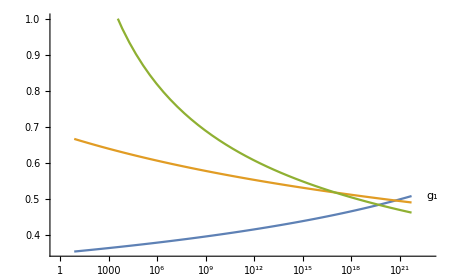

```mathematica
$=Sqrt[1/{$1 ,$2,$3}];
LogLinearPlot[$,{μ,Exp[2],Exp[50]},
PlotLabels->{Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]}]
```